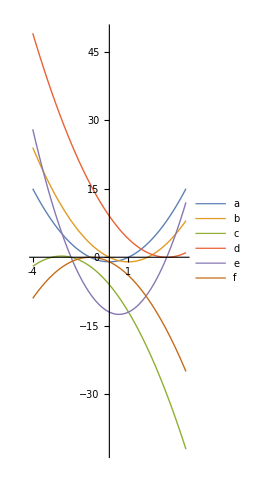

```mathematica
Plot[{x^2-1,x^2-2x,-x^2-5x-6,(x-3)^2,2(x+2)(x-3),-(x+1)^2},{x,-4,4},AspectRatio->Full,Ticks->{Range[-4,4],Automatic},PlotStyle->Thickness[.0025],PlotLegends->Alphabet[]]
```

```mathematica
RandomSample[{x^2-1,x^2-2x,-x^2-5x-6,(x-3)^2,2(x+2)(x-3),-(x+1)^2}]//Expand//TraditionalForm
```

{x^2-6 x+9,x^2-2 x,2 x^2-2 x-12,x^2-1,-x^2-2 x-1,-x^2-5 x-6}

```mathematica
Expand[(x+44)(x-55)]//TraditionalForm
```

x^2-11 x-2420

```mathematica
Reduce[(x+44)(x-55)≤0]
```

-44≤x≤55

```mathematica
Reduce[3x - 2x^2 >= 2]
```

False

```mathematica
Reduce[(x+1)(x+2)<(2x+3)(x+4)]
```

x<-4-√6||x>-4+√6

```mathematica
Reduce[x^2+2x≤-1,x]
```

x==-1

```mathematica
Expand[(x+2)(x^2+1)]//TraditionalForm
```

x^3+2 x^2+x+2

```mathematica
Reduce[(x+2)(x^2+1)≥0]
```

x≥-2

```mathematica
Reduce[(x^2+4x-2)<0]
```

-2-√6<x<-2+√6

```mathematica
Reduce[(x^2+4x-2)(x^2+4x+2)>0]
```

x<-2-√6||-2-√2<x<-2+√2||x>-2+√6

```mathematica
Reduce[(x^2+4x-2)/(x^2+4x+2)>=0]
```

x≤-2-√6||-2-√2<x<-2+√2||x≥-2+√6

```mathematica
Discriminant[2x^2+7x+c,x]
```

49-8 c